1. NALOGA

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1,-1},{3,1}]
d3 = Daljica[{-1, 2},{3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]]:= Norm[BB - AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_, BB_]]:= Line[{AA, BB}]
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
?Line
```

Line[{p_1,p_2,…}] represents the line segments joining a sequence for points p_i.
Line[{{p_11,p_12,…},{p_21,…},…}] represents a collection of lines.

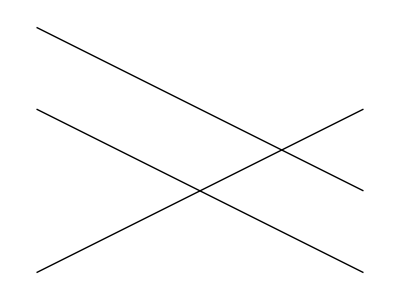

```mathematica
Narisi[d_Daljica]:=Graphics[Slika[d]]
Narisi[d__Daljica]:=Graphics[Map[Slika, List[d]]]
Narisi[d, d2, d3]
```

```mathematica
ClearAll[EnacbaNosilke, x, y]
```

```mathematica
EnacbaNosilke[Daljica[AA_, BB_]]:=Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2-x1);
n = y1 - k *x1;
y ==  k x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

2. NALOGA

```mathematica
Clear[Presek, s, r]
```

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:=Module[{resitev}, resitev = Solve[{AA + r * (BB - AA)== CC + s * (DD - CC), s ≥ 0, s≤ 1, r ≥ 0, r≤ 1},{s, r}]
]
Presek[d, d]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{s→ConditionalExpression[r,0≤r≤1]}}

```mathematica
d
d2
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

```mathematica
Presek[d, d2]
```

{{s→1/2,r→1/2}}

```mathematica
Presek[d2, d3]
```

{{s→3/4,r→3/4}}

```mathematica
d3
```

Daljica[{-1,2},{3,0}]

3. NALOGA

```mathematica
m1 = Mnogokotnik[{0,0},{1,1},{0,3},{-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
Slika[Mnogokotnik[t__]]:=Line[{t}]
```

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2}}]

```mathematica
Clear[Narisi]
```

```mathematica
?Append
```

Append[expr,elem] gives expr with elem appended. 
Append[elem] represents an operator form of Append that can be applied to an expression.

```mathematica
m1 = Append[m1, First[m1]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Narisi[m__Mnogokotnik]:= Graphics[Map[Slika, List[m]]]
```

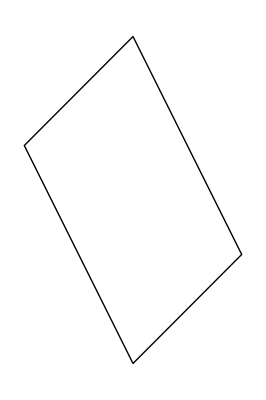

```mathematica
Narisi[m1]
```

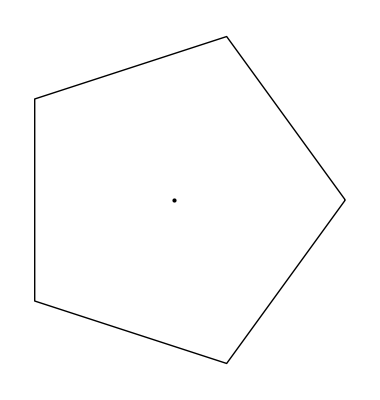

```mathematica
PravilniNKotnik[n_,r_]:=Graphics[{Line[Table[{r*Cos[(2 Pi*i)/n],r*Sin[(2 Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
p5=PravilniNKotnik[5,2]
```

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
PravilniNKotnik[n_, r_, phi_]:= Manipulate[Graphics[
{Line[Table[{r*Cos[(2Pi*i + x)/n],r*Sin[(2Pi*i + x)/n]},{i,0,n}]],Point[{0,0}]}], {x, 0, Pi}]
```

```mathematica
PravilniNKotnik[5, 2, Pi]
```

```mathematica
?Partition
```

Partition[list,n] partitions list into nonoverlapping sublists of length n. 
Partition[list,n,d] generates sublists with offset d. 
Partition[list,{n_1,n_2,…}] partitions a nested list into blocks of size n_1×n_2×….
Partition[list,{n_1,n_2,…},{d_1,d_2,…}] uses offset d_i at level i in list. 
Partition[list,n,d,{k_L,k_R}] specifies that the first element of list should appear at position k_L in the first sublist, and the last element of list should appear at or after position k_R in the last sublist. If additional elements are needed, Partition fills them in by treating list as cyclic. 
Partition[list,n,d,{k_L,k_R},x] pads if necessary by repeating the element x. 
Partition[list,n,d,{k_L,k_R},{x_1,x_2,…}] pads if necessary by cyclically repeating the elements x_i. 
Partition[list,n,d,{k_L,k_R},{}] uses no padding, and so can yield sublists of different lengths. 
Partition[list,nlist,dlist,{klist_L,klist_R},padlist] specifies alignments and padding in a nested list.

```mathematica
Daljice[Mnogokotnik[t__]]:=Partition[{t}, {2, 2}, 1]
```

```mathematica
m1
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Daljice[m1]
```

{{{{0,0},{1,1}}},{{{1,1},{0,3}}},{{{0,3},{-1,2}}},{{{-1,2},{0,0}}}}

4. NALOGA

```mathematica
d = Daljica[{-1,1},{3,-1}];
d2 = Daljica[{-1,-1},{3,1}];
d3 = Daljica[{-1, 2},{3, 0}];
m1;
```

```mathematica
?Module
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

```mathematica
Presek[m_Mnogokotnik[AA_, BB_], d_Daljica[CC_,DD_]]:= Module[{a, b},
a = Daljice[m1];
b = d;
resitev = Solve[{AA + r * (BB - AA)== CC + s * (DD - CC), s ≥ 0, s≤ 1, r ≥ 0, r≤ 1}, {x, y}]]
```

```mathematica
Presek[m1, d]
```

```mathematica
{}
Presek[m1, d2]
```

{}

5. NALOGA

```mathematica
?Outer
```

Outer[f,list_1,list_2,…] gives the generalized outer product of the list_i, forming all possible combinations of the lowest-level elements in each of them, and feeding them as arguments to f. 
Outer[f,list_1,list_2,…,n] treats as separate elements only sublists at level n in the list_i. 
Outer[f,list_1,list_2,…,n_1,n_2,…] treats as separate elements only sublists at level n_i in the corresponding list_i.

```mathematica
?Flatten
```

Flatten[list] flattens out nested lists. 
Flatten[list,n] flattens to level n. 
Flatten[list,n,h] flattens subexpressions with head h. 
Flatten[list,{{s_11,s_12,…},{s_21,s_22,…},…}] flattens list by combining all levels s_ij to make each level i in the result.

```mathematica
ClearAll[f, a, b, d]
```

```mathematica
VsiPari[f_, sez1_, sez2_]:= Flatten[Outer[f, sez1, sez2], 1]
```

```mathematica
VsiPari[f, {1, 2,3 },{a, b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
q= Outer[f, {1, 2,3 },{a, b}]
```

{{f[1,a],f[1,b]},{f[2,a],f[2,b]},{f[3,a],f[3,b]}}

```mathematica
Flatten[q]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}]
```

{b,2,1,3,4,f,g,h}

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}, 1]
```

{b,2,1,3,{4},f,{g,h}}

```mathematica
Flatten[{{b, 2},{1, 3, {4}},{f, {g, h}}}, 2]
```

{b,2,1,3,4,f,g,h}

```mathematica
Outer[{b, 2},{1, 3, {4}},{f, {g, h}}]
```

{{{b,2}[1,f],{{b,2}[1,g],{b,2}[1,h]}},{{b,2}[3,f],{{b,2}[3,g],{b,2}[3,h]}},{{{b,2}[4,f],{{b,2}[4,g],{b,2}[4,h]}}}}

```mathematica
Outer[f,{a,b},{x,y,z}]
```

{{f[a,x],f[a,y],f[a,z]},{f[b,x],f[b,y],f[b,z]}}

```mathematica
m2 = Mnogokotnik[{0,0},{1,1},{0,3},{-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
m3 = Mnogokotnik[{0,1},{1,2},{2,3},{-5, 2}]
```

Mnogokotnik[{0,1},{1,2},{2,3},{-5,2}]

```mathematica
Presek[m1_Mnogokotnik, m2_Mnogokotnik]:= VsiPari[f, m1, m2]
```

```mathematica
Presek[m1, m2]
Presek[m1, m3]
```

Mnogokotnik[f[{0,0},{0,0}],f[{0,0},{1,1}],f[{0,0},{0,3}],f[{0,0},{-1,2}],f[{1,1},{0,0}],f[{1,1},{1,1}],f[{1,1},{0,3}],f[{1,1},{-1,2}],f[{0,3},{0,0}],f[{0,3},{1,1}],f[{0,3},{0,3}],f[{0,3},{-1,2}],f[{-1,2},{0,0}],f[{-1,2},{1,1}],f[{-1,2},{0,3}],f[{-1,2},{-1,2}],f[{0,0},{0,0}],f[{0,0},{1,1}],f[{0,0},{0,3}],f[{0,0},{-1,2}]]

Mnogokotnik[f[{0,0},{0,1}],f[{0,0},{1,2}],f[{0,0},{2,3}],f[{0,0},{-5,2}],f[{1,1},{0,1}],f[{1,1},{1,2}],f[{1,1},{2,3}],f[{1,1},{-5,2}],f[{0,3},{0,1}],f[{0,3},{1,2}],f[{0,3},{2,3}],f[{0,3},{-5,2}],f[{-1,2},{0,1}],f[{-1,2},{1,2}],f[{-1,2},{2,3}],f[{-1,2},{-5,2}],f[{0,0},{0,1}],f[{0,0},{1,2}],f[{0,0},{2,3}],f[{0,0},{-5,2}]]

6. NALOGA

a) Izračunaj vektorski produkt V1 in V2, če imaš podane 3 točke.

```mathematica
AA:={2, 2, 5}
BB := {5, -2, 1}
CC := {0, 0, 3}
vektor1 [AA_, BB_]:= BB - AA
vektor2[AA_, CC_]:=CC-AA
```

```mathematica
V1 = vektor1[AA, BB]
V2 =vektor2[BB, CC]
```

{3,-4,-4}

{-5,2,2}

```mathematica
V3 =Cross[V1, V2]
```

{0,14,-14}

b) Nariši vektorje V1, V2 in pravokotnico na oba vektorja

```mathematica
vektorji = {{AA, BB},{AA, CC},{AA, V3}}
```

{{{2,2,5},{5,-2,1}},{{2,2,5},{0,0,3}},{{2,2,5},{0,14,-14}}}

```mathematica
Graphics3D[Map[Line, vektorji ]]
```

-Graphics3D-